```mathematica
θ0[h_,R_,L_]:=θ/.NSolve[h-R(1+Sin[θ])==(L/2-R Cos[θ])Tan[2θ],θ]
```

```mathematica
θ0[1.3,1,6]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{-3.09885,-1.35596,0.0597356,1.45281}

```mathematica
θ0[h_,R_,L_]:=θ/.FindRoot[h-R(1+Sin[θ])==(L/2-R Cos[θ])Tan[2θ],{θ,0.001}]
```

```mathematica
θ0[1.3,1,6]
```

0.0597356

```mathematica
%*180/π
```

3.4226

```mathematica
f[h_,R_,L_,θ_]:=h-R(1+Sin[θ])-(L/2-R Cos[θ])Tan[2θ]
```

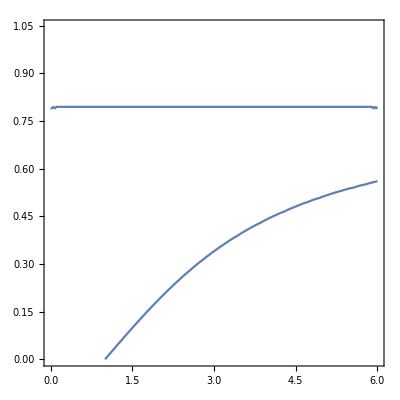

```mathematica
ContourPlot[f[h,1,6,θ]==0,{h,0,6},{θ,0,π/3}]
```

```mathematica
3 √3//N
```

5.19615

```mathematica
f[3 √3,1,6,π/6]//N
```

0.

```mathematica
f[1,1,6,0]//N
```

0.

```mathematica
π/6//N
```

0.523599

```mathematica
f[2,1,6,0.19089319211243522]
```

4.44089×10^-16

```mathematica
Sin[0.19089319211243522]
```

0.189736

```mathematica
f[3 √3,1,6,π/6]//N
```

0.

```mathematica
p0[h_,R_,L_]:=p/.NSolve[((h-R)√(1+p^2)-R)(1-p^2)==2p(L/2(1+p^2)-R √(1+p^2)),p]
```

```mathematica
p0[1.3,1,6]
```

{0.209575+0.908088 ⅈ,0.209575-0.908088 ⅈ,-0.163827}

```mathematica
ArcTan[p0[1.3,1,6][[3]]]
```

-0.162384

```mathematica
(* Unique zero in[IntervalArithmetic.Interval(-0.2852575176735223,-0.2852575176734356),IntervalArithmetic.Interval(0.2892750985644935,0.2892750985645683)] *)
```

```mathematica
Sin[0.289275]
```

0.285257

```mathematica
0.289275*180/π
```

16.5742

```mathematica
f[1.3,1,6,0.2892750985644935]
```

-1.31859

```mathematica
(*****************************************************************************************)
```

```mathematica
(* General Birkhoff for an arbitrary system of disks of radius 1 *)
```

```mathematica
c0:={{0,0},{6,0},{3,3 √3}}
```

```mathematica
c1:={{0,0},{6,0},{3,1.3}}
```

```mathematica
r[c_]:=Table[Norm[c[[i]]-c[[j]]],{i,Length[c]},{j,Length[c]}]
```

```mathematica
r[c0]
```

{{0,6,6},{6,0,6},{6,6,0}}

```mathematica
(* Using "atan2" here *)
```

```mathematica
α[c_]:=Quiet[Table[ArcTan[(c[[j]]-c[[i]])[[1]],(c[[j]]-c[[i]])[[2]]],{i,Length[c]},{j,Length[c]}]]
```

```mathematica
α[c0]
```

{{Indeterminate,0,π/3},{π,Indeterminate,(2 π)/3},{-(2 π)/3,-π/3,Indeterminate}}

```mathematica
α[c1]
```

{{Indeterminate,0,0.408908},{π,Indeterminate,2.73268},{-2.73268,-0.408908,π/2}}

```mathematica
ωnext[ω_,θ_,c_,n_,m_]:=ω-r[c][[n]][[m]] (ω Cos[θ-α[c][[n]][[m]]]+√(1-ω^2)Sin[θ-α[c][[n]][[m]]])
```

```mathematica
T[ω_,θ_,c_,n_,m_]:={ωnext[ω,θ,c,n,m],Mod[θ+π+ArcSin[ω] +ArcSin[ωnext[ω,θ,c,n,m]] ,2π]}
```

```mathematica
T0[x_,c_,n_,m_]:=T[x[[1]],x[[2]],c,n,m]
```

```mathematica
T0[{Sin[-π/6],π/6},c0,1,2]
```

{-1/2,(5 π)/6}

```mathematica
T0[T0[{Sin[-π/6],π/6},c0,1,2],c0,2,3]
```

{-1/2,(3 π)/2}

```mathematica
T0[T0[T0[{Sin[-π/6],π/6},c0,1,2],c0,2,3],c0,3,1]
```

{-1/2,π/6}

```mathematica
T1231[x_,c_]:=T0[T0[T0[x,c,1,2],c,2,3],c,3,1]
```

```mathematica
T1321[x_,c_]:=T0[T0[T0[x,c,1,3],c,3,2],c,2,1]
```

```mathematica
orbit123[c_]:=FindInstance[T0[T0[T0[{x1,x2},c,1,2],c,2,3],c,3,1][[1]]==x1&&T0[T0[T0[{x1,x2},c,1,2],c,2,3],c,3,1][[2]]==x2,{x1,x2},Reals]
```

```mathematica
orbit123[c0]
```

$Aborted

```mathematica
orbit123[c1]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x1→-0.56-2.18849×10^-15 ⅈ,x2→0.4+2.30867×10^-15 ⅈ}

```mathematica
T1231[{-0.5,π/6},c0]
```

{-0.5,0.523599}

```mathematica
T1321[{0.5,π/6},c0]
```

{0.5,0.523599}

```mathematica
T1231[{-0.285257517674,0.289275098565},c1]
```

{-0.285258,0.289275}

```mathematica
(* This is the new value with "atan2" *)
```

```mathematica
T1231[{-0.285257517674,0.289275098565},c1]
```

{-1.14785,1.53227+0.537305 ⅈ}

```mathematica
(* Not the same! Let's check the one with analytical formula for isosceles system (below) *)
```

```mathematica
T1231[{-Sin[0.059735608013714116],0.059735608013714116},c1]
```

{-2.39503,3.5759+1.5198 ⅈ}

```mathematica
T1231[{-0.3731362044979274,0.38238707697322843},c1]
```

{-12.2878+4.33872 ⅈ,4.28797+5.20597 ⅈ}

```mathematica
Sin[0.38238707697322843]
```

0.373136

```mathematica
0.38238707697322843*180/π
```

21.9092

```mathematica
r[c1]
```

{{0,6,3.26956},{6,0,3.26956},{3.26956,3.26956,0.}}

```mathematica
α[c1]
```

{{Indeterminate,0,0.408908},{0,Indeterminate,-0.408908},{0.408908,-0.408908,Indeterminate}}

```mathematica
x1:={-0.3731362044979262,0.38238707697323093}
```

```mathematica
T0[x1,c1,1,2]
```

{-0.373136,2.75921}

```mathematica
T0[T0[x1,c1,1,2],c1,2,3]
```

{-0.721539,4.71239}

```mathematica
x2:={-0.37313620449792995,2.7592055766165657}
```

```mathematica
T0[x2,c1,2,3]
```

{-0.721539,4.71239}

```mathematica
r[c1][[2]][[3]]
```

3.26956

```mathematica
α[c1][[2]][[3]]
```

-0.408908

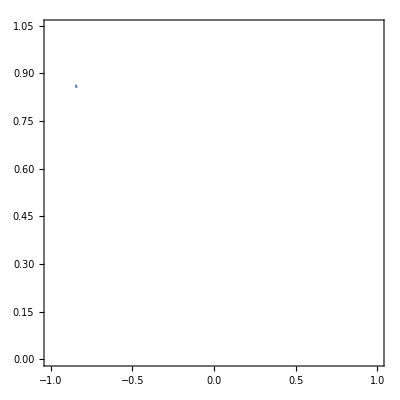

```mathematica
ContourPlot[T1231[{ω,θ},c1]=={ω,θ},{ω,-1,1},{θ,0,π/3}]
```

```mathematica
ContourPlot[T1231[{ω,θ},c0]==0,{ω,-1,1},{θ,0,π/3}]
```

$Aborted

```mathematica
(* Analytical solution for isosceles orbit *)
```

```mathematica
p/.Solve[(p r-(d-1)(1-p^2))^2==p^2(1+p^2),p]
```

```mathematica
sol[6,1.3]
```

{0.0427731+0. ⅈ,0.0598068+0. ⅈ,-4.58279+0. ⅈ,8.43625+0. ⅈ}

```mathematica
ArcTan[0.04277314680302197]
```

0.0427471

```mathematica
ArcTan[0.059806761952484626]
```

0.0597356

```mathematica
sol1[r_,d_]:=θ/.NSolve[Tan[2θ]==(d-1-Sin[θ])/(r/2-Cos[θ]),θ]
```

```mathematica
sol1[6,1.3]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{-3.09885,-1.35596,0.0597356,1.45281}

```mathematica
T1231[{-Sin[0.059735608013714046],0.059735608013714046},c1]
```

{-0.0597001,0.0597356}

```mathematica
(* Yes! The problem was in α which used "atan" instead of "atan2" *)
```

```mathematica
(* Analytical solution for isosceles 1231: ω = sin θ, and θ is given by the formula below *)
```

```mathematica
θisos[r_,d_]:=Re[ArcTan[-(-r+d r)/(2 (-2+d) d)-1/2 √((-r+d r)^2/((-2+d)^2 d^2)-(-3+4 d-2 d^2+r^2)/((-2+d) d)+(-3+4 d-2 d^2+r^2)/(3 (-2 d+d^2))+(2^(1/3) (3-8 d+4 d^2+r^2)^2)/(3 (-2+d) d (-54-216 d+1260 d^2-2176 d^3+1824 d^4-768 d^5+128 d^6+54 r^2-288 d r^2+528 d^2 r^2-384 d^3 r^2+96 d^4 r^2+18 r^4-48 d r^4+24 d^2 r^4+2 r^6+√(69984 d-423792 d^2+1107648 d^3-1617840 d^4+1423872 d^5-753408 d^6+221184 d^7-27648 d^8-11664 r^2+85536 d r^2-250128 d^2 r^2+373248 d^3 r^2-300672 d^4 r^2+124416 d^5 r^2-20736 d^6 r^2-3888 r^4+18144 d r^4-29808 d^2 r^4+20736 d^3 r^4-5184 d^4 r^4-432 r^6+864 d r^6-432 d^2 r^6))^(1/3))+1/(3 2^(1/3) (-2+d) d)(-54-216 d+1260 d^2-2176 d^3+1824 d^4-768 d^5+128 d^6+54 r^2-288 d r^2+528 d^2 r^2-384 d^3 r^2+96 d^4 r^2+18 r^4-48 d r^4+24 d^2 r^4+2 r^6+√(69984 d-423792 d^2+1107648 d^3-1617840 d^4+1423872 d^5-753408 d^6+221184 d^7-27648 d^8-11664 r^2+85536 d r^2-250128 d^2 r^2+373248 d^3 r^2-300672 d^4 r^2+124416 d^5 r^2-20736 d^6 r^2-3888 r^4+18144 d r^4-29808 d^2 r^4+20736 d^3 r^4-5184 d^4 r^4-432 r^6+864 d r^6-432 d^2 r^6))^(1/3))+1/2 √((2 (-r+d r)^2)/((-2+d)^2 d^2)-(-3+4 d-2 d^2+r^2)/((-2+d) d)-(-3+4 d-2 d^2+r^2)/(3 (-2 d+d^2))-(2^(1/3) (3-8 d+4 d^2+r^2)^2)/(3 (-2+d) d (-54-216 d+1260 d^2-2176 d^3+1824 d^4-768 d^5+128 d^6+54 r^2-288 d r^2+528 d^2 r^2-384 d^3 r^2+96 d^4 r^2+18 r^4-48 d r^4+24 d^2 r^4+2 r^6+√(69984 d-423792 d^2+1107648 d^3-1617840 d^4+1423872 d^5-753408 d^6+221184 d^7-27648 d^8-11664 r^2+85536 d r^2-250128 d^2 r^2+373248 d^3 r^2-300672 d^4 r^2+124416 d^5 r^2-20736 d^6 r^2-3888 r^4+18144 d r^4-29808 d^2 r^4+20736 d^3 r^4-5184 d^4 r^4-432 r^6+864 d r^6-432 d^2 r^6))^(1/3))-1/(3 2^(1/3) (-2+d) d)(-54-216 d+1260 d^2-2176 d^3+1824 d^4-768 d^5+128 d^6+54 r^2-288 d r^2+528 d^2 r^2-384 d^3 r^2+96 d^4 r^2+18 r^4-48 d r^4+24 d^2 r^4+2 r^6+√(69984 d-423792 d^2+1107648 d^3-1617840 d^4+1423872 d^5-753408 d^6+221184 d^7-27648 d^8-11664 r^2+85536 d r^2-250128 d^2 r^2+373248 d^3 r^2-300672 d^4 r^2+124416 d^5 r^2-20736 d^6 r^2-3888 r^4+18144 d r^4-29808 d^2 r^4+20736 d^3 r^4-5184 d^4 r^4-432 r^6+864 d r^6-432 d^2 r^6))^(1/3)-((16 (-r+d r))/((-2+d) d)-(8 (-r+d r)^3)/((-2+d)^3 d^3)+(8 (-r+d r) (-3+4 d-2 d^2+r^2))/((-2+d)^2 d^2))/(4 √((-r+d r)^2/((-2+d)^2 d^2)-(-3+4 d-2 d^2+r^2)/((-2+d) d)+(-3+4 d-2 d^2+r^2)/(3 (-2 d+d^2))+(2^(1/3) (3-8 d+4 d^2+r^2)^2)/(3 (-2+d) d (-54-216 d+1260 d^2-2176 d^3+1824 d^4-768 d^5+128 d^6+54 r^2-288 d r^2+528 d^2 r^2-384 d^3 r^2+96 d^4 r^2+18 r^4-48 d r^4+24 d^2 r^4+2 r^6+√(69984 d-423792 d^2+1107648 d^3-1617840 d^4+1423872 d^5-753408 d^6+221184 d^7-27648 d^8-11664 r^2+85536 d r^2-250128 d^2 r^2+373248 d^3 r^2-300672 d^4 r^2+124416 d^5 r^2-20736 d^6 r^2-3888 r^4+18144 d r^4-29808 d^2 r^4+20736 d^3 r^4-5184 d^4 r^4-432 r^6+864 d r^6-432 d^2 r^6))^(1/3))+1/(3 2^(1/3) (-2+d) d)(-54-216 d+1260 d^2-2176 d^3+1824 d^4-768 d^5+128 d^6+54 r^2-288 d r^2+528 d^2 r^2-384 d^3 r^2+96 d^4 r^2+18 r^4-48 d r^4+24 d^2 r^4+2 r^6+√(69984 d-423792 d^2+1107648 d^3-1617840 d^4+1423872 d^5-753408 d^6+221184 d^7-27648 d^8-11664 r^2+85536 d r^2-250128 d^2 r^2+373248 d^3 r^2-300672 d^4 r^2+124416 d^5 r^2-20736 d^6 r^2-3888 r^4+18144 d r^4-29808 d^2 r^4+20736 d^3 r^4-5184 d^4 r^4-432 r^6+864 d r^6-432 d^2 r^6))^(1/3))))]]
```

```mathematica
θisos[6,1.3]
```

0.0597356

```mathematica
T1231[{-Sin[θisos[6,1.3]],θisos[6,1.3]},c1]
```

{-0.0597001,0.0597356}

```mathematica
{-Sin[θisos[6,1.3]],θisos[6,1.3]}
```

{-0.0597001,0.0597356}